#### Simple control problem

```mathematica
ClearAll["Global`*"];

(*Time domain and target*)
T=3;
x0=1;
xStar[t_]:=Exp[-3t];

(**)

(*Training hyperparameters*)
ηmax=0.5;
c=0.5;
β=1;
nIter=100;
θ=-5; (*initial guess*)

θHist={θ};
lossHist={};

(*Function to compute loss and gradient for given θ*)
computeLossAndGrad[θ_]:=Module[{xSol,λSol,loss,gradJ},
xSol=NDSolveValue[{x'[t]==θ x[t],x[0]==x0},x,{t,0,T},AccuracyGoal->1,PrecisionGoal->4];
λSol=NDSolveValue[{λ'[t]==-θ λ[t]+2 (xSol[t]-xStar[t]),λ[T]==0},λ,{t,T,0},AccuracyGoal->1,PrecisionGoal->4];
gradJ=NIntegrate[λSol[t] *xSol[t],{t,0,T}];
loss=NIntegrate[(xSol[t]-xStar[t])^2,{t,0,T}];
{loss,gradJ}];

(*Initial loss/grad*)
{loss,grad}=computeLossAndGrad[θ];

(*Training loop with adaptive step size*)
AbsoluteTiming[Do[η=ηmax;
{loss,grad}=computeLossAndGrad[θ];
(*Backtracking line search*)

While[True,
θtrial=θ+η grad;
{losstrial,grad}=computeLossAndGrad[θtrial];
If[losstrial<=loss-c η grad^2,Break[],η=β η;
If[η<10^-6,Break[]]]];
θ=θ+η grad;
AppendTo[θHist,θ];
AppendTo[lossHist,loss];,{i,nIter}]
]

(*Final learned x(t)*)
xLearned[t_]=NDSolveValue[{x'[t]==θ x[t],x[0]==x0},x,{t,0,T}][t];

(*Final learned x(t)*)
xLearned[t_]=NDSolveValue[{x'[t]==θ x[t],x[0]==x0},x,{t,0,T}][t];

(*Plot learned vs target trajectory*)
plt1=Plot[{xLearned[t],xStar[t]},{t,0,T},PlotLegends->{"Learned x(t)","Target x*(t)"},PlotStyle->{Thick,Dashed},PlotRange->Full,PlotLabel->"Trajectory Fit"];

(*Plot loss over iterations*)
plt2=ListLinePlot[lossHist,PlotLabel->"Loss J(θ) over iterations",AxesLabel->{"Iteration","Loss"},PlotMarkers->Automatic];

(*Plot θ over iterations*)
plt3=ListLinePlot[θHist,PlotLabel->"θ over iterations",AxesLabel->{"Iteration","θ"},PlotMarkers->Automatic];

(*Show all plots*)
GraphicsGrid[{{plt1},{plt2,plt3}}]
```

{12.1881,Null}

-Graphics-

#### Derivative space

155

(187.652 | 2069.83 | 43.9539
2069.83 | 33.8525 | 1.43775
43.9539 | 1.43775 | 66664.2)

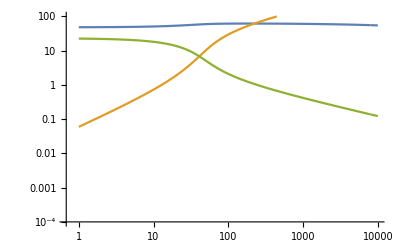

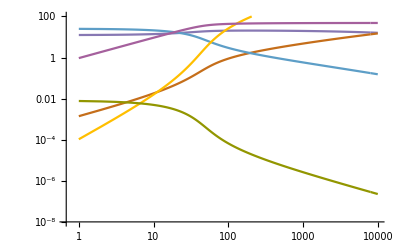

```mathematica
ClearAll["Global`*"];

n=3;

(*Variables*)
cVars=Array[c,n];

seed = RandomInteger[1000];
(*seed = 794;*)
seed = 155
SeedRandom[seed];  


(*reproducibility*)
mVals=RandomReal[{0.1,100.0},n];

kVals=RandomReal[{0.01,10.0},{n,n}];

(*Parameters for the log-normal distribution*)
μ=1;       (*Mean of the underlying normal distribution*)
σ=5;       (*Standard deviation*)

(*Sample kVals as log-normally distributed*)
kVals=RandomVariate[LogNormalDistribution[μ,σ],{n,n}];
kVals[[1,2]]=2kVals[[1,3]] kVals[[2,2]]/kVals[[2,3]];
Do[If[i>j,kVals[[i,j]]=kVals[[j,i]]],{i,n},{j,n}];
kVals//MatrixForm

(*Assign random positive starting point for each variable*)
initialGuess=Table[cVars[[i]]->RandomReal[{0.1,2.0}],{i,1,n}];

mInd = 2;
mRange = Range[0,10000,1];
solArray = {};
soldijArray = {};
Do[
mVals[[mInd]]=mv;
eqnsSym=Table[Sum[cVars[[i]] *cVars[[j]] *kVals[[i,j]]^-1,{j,1,n}]+cVars[[i]]-mVals[[i]],{i,1,n}];
sol=FindRoot[eqnsSym, Table[{cVars[[i]],cVars[[i]]/.initialGuess},{i,1,n}], AccuracyGoal->5, PrecisionGoal->10];
cSol =  cVars/.sol;
AppendTo[solArray,cSol];

dij=kVals^-1*KroneckerProduct[cSol, cSol];

upperTriangleList=Flatten[Table[dij[[i,j]],{i,1,n},{j,i,n}]];
AppendTo[soldijArray,upperTriangleList];

initialGuess=sol;
,{mv,mRange}];

Show[
Table[
ListLogLogPlot[
Transpose[{mRange,solArray[[All,k]]}],Joined->True,PlotRange->{0.0001,100},PlotStyle->ColorData[97][k] 
],{k,1,n}]
]

Show[Table[
ListLogLogPlot[
Transpose[{mRange,soldijArray[[All,k]]}],Joined->True,PlotRange->{10^-8,100},PlotStyle->ColorData[97][k+n+1] 
],{k,1,Dimensions[soldijArray][[2]]}]
]

(*Show[
Table[
ListPlot[
Transpose[{mRange,solArray[[All,k]]}],Joined->True,PlotRange->{0.001,100},PlotStyle->ColorData[97][k] 
],{k,1,n}]
]

Show[Table[
ListPlot[
Transpose[{mRange,soldijArray[[All,k]]}],Joined->True,PlotRange->{10^-8,100},PlotStyle->ColorData[97][k+n+1] 
],{k,1,Dimensions[soldijArray][[2]]}]
]*)
```

```mathematica
mVars=Array[m,n];
cVals = {1,100,1};
initialGuess=Table[mVars[[i]]->RandomReal[{0.1,2.0}],{i,1,n}];
eqnsSym = Table[Sum[cVals[[i]] *cVals[[j]] *kVals[[i,j]]^-1,{j,1,n}]+cVals[[i]]-mVars[[i]],{i,1,n}]
sol=FindRoot[eqnsSym, Table[{mVars[[i]],mVars[[i]]/.initialGuess},{i,1,n}], AccuracyGoal->5, PrecisionGoal->10]
```

{1.07639-m[1],465.001-m[2],70.576-m[3]}

{m[1]→1.07639,m[2]→465.001,m[3]→70.576}

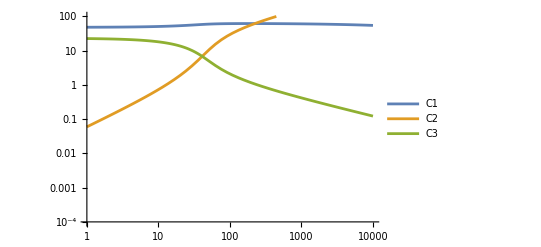

```mathematica
(*Step 1:Set problem size and target column*)
nd=n;           (*number of components*)
mInd=2;         (*column of J^-1 to extract*)


(*kVals=RandomVariate[LogNormalDistribution[μ,σ],{n,n}];
Do[If[i>j,kVals[[i,j]]=kVals[[j,i]]],{i,n},{j,n}];*)

(*kVals=kValsList[[4]];*)


mRange = Range[0,10000,1];
m0 = mVals;
m0[[mInd]]=mRange[[1]];

eqnsSym=Table[Sum[cVars[[i]] *cVars[[j]] *kVals[[i,j]]^-1,{j,1,n}]+cVars[[i]]-m0[[i]],{i,1,n}];
sol=FindRoot[eqnsSym, Table[{cVars[[i]],cVars[[i]]/.initialGuess},{i,1,n}], AccuracyGoal->5, PrecisionGoal->10];
cSol =  cVars/.sol;


kkFlatVals=Flatten[kVals]^-1;

(*Step 2:Define symbolic matrices and compute grads symbolically*)

Qf=Table[CC[i]*KK[i,j],{i,nd},{j,nd}];
Qd=DiagonalMatrix[Table[1+Sum[KK[i,j]*CC[j],{j,nd}],{i,nd}]];
symmetryRules=Flatten[Table[If[i>j,KK[i,j]->KK[j,i],Nothing],{i,nd},{j,nd}]];
Qmat=Qf+Qd/. symmetryRules;
JInv=Simplify[Inverse[Qmat]];
gradsExpr=Simplify[JInv[[All,mInd]]];  (*symbolic expression*)

(*Step 3:Turn symbolic grads into a fast numeric function*)
ccSyms=Table[CC[i],{i,nd}];
kkSyms=Flatten[Table[KK[i,j],{i,nd},{j,nd}]];
gradFun=Function[{ccVec,kkFlat},Evaluate[Evaluate[gradsExpr/. Thread[ccSyms->ccVec]]/. Thread[kkSyms->kkFlat]]];

(*Step 4:Define fixed KK values and fast vector field*)

fVecFast[cc_]:=gradsExpr/.Thread[kkSyms->kkFlatVals]/.Thread[ccSyms->cc];

(*Step 5:Define and solve ODE system*)
vars=Array[C,nd];    
odes=Table[vars[[i]]'[t]==fVecFast[Table[vars[[j]][t],{j,nd}]][[i]],{i,nd}];
initConds=Thread[Table[vars[[i]][0],{i,nd}]==cSol];
sol=NDSolve[Join[odes,initConds],vars,{t,mRange}];

(*Step 6:Plot the trajectories*)
LogLogPlot[Evaluate[Table[vars[[i]][t]/. sol[[1]],{i,nd}]],{t,1,mRange[[-1]]},PlotLegends->Table["C"<>ToString[i],{i,nd}],PlotRange->{0.0001,100},PlotRange->All]
```

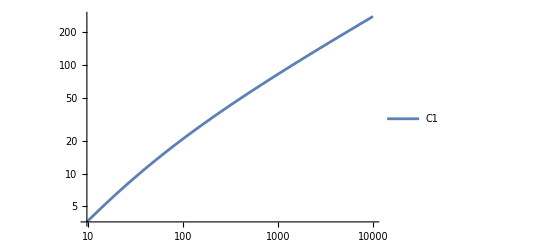

```mathematica
LogLogPlot[Evaluate[vars[[3]][t]/. sol[[1]]],{t,mRange[[1]],mRange[[-1]]},PlotLegends->Table["C"<>ToString[i],{i,nd}],PlotRange->Full,PlotRange->All]
```

```mathematica
exprs=Adjugate[Qmat][[;;,mInd]]/. Thread[kkSyms->Flatten[kVals]^-1]

cMin = 0.0001;
cMax = 1;
Show[
ContourPlot3D[exprs,{CC[1],cMin,cMax},{CC[2],cMin,cMax},{CC[3],cMin,cMax},AxesLabel->{"c1","c2","c3"},PlotPoints->10],
ParametricPlot3D[Evaluate[Table[vars[[i]][t]/. sol[[1]],{i,nd}]],{t,mRange[[1]],mRange[[-1]]}, PlotStyle->Directive[Black,Thickness[0.008]]]
]
```

{-0.000483131 CC[1]-0.0000109918 CC[1]^2-0.000336033 CC[1] CC[2]+0.0158241 CC[1] CC[3],(1+0.0227511 CC[1]+0.695532 CC[2]+0.0000300011 CC[3]) (1+0.010658 CC[1]+0.000483131 CC[2]+0.0227511 CC[3])-0.000517614 CC[1] CC[3],-0.695532 CC[3]-0.00740202 CC[1] CC[3]-0.000336033 CC[2] CC[3]-0.0158241 CC[3]^2}

-Graphics3D-

-Graphics3D-

```mathematica
expr=-0.0000109918*CC[1]^2+0.333333*CC[2]*CC[3];

RationalizeMonomials[expr]
```

-0.0000109918 CC[1]^2+0.333333 CC[2] CC[3]

```mathematica
DeepRationalize[poly1]
```

-(442 CC[1])/914865-(33 CC[1]^2)/3002242-(161 CC[1] CC[2])/479119+(16041 CC[1] CC[3])/1013705

```mathematica
Rationalize[-0.0004831313905123825 ,10^-10]
```

-53/109701

```mathematica
CCVars = Table[CC[i],{i,1,n}];
poly1 = exprs[[1]]
monList = MonomialList[poly1]
CoefficientList[monList[[1]],CCVars]
```

-0.000483131 CC[1]-0.0000109918 CC[1]^2-0.000336033 CC[1] CC[2]+0.0158241 CC[1] CC[3]

{-0.0000109918 CC[1]^2,-0.000336033 CC[1] CC[2],0.0158241 CC[1] CC[3],-0.000483131 CC[1]}

{{{0}},{{0}},{{-0.0000109918}}}

```mathematica
DeepRationalize[exprs[[3]]]
```

-(757036 CC[3])/1088427-(11252 CC[1] CC[3])/1520125-(161 CC[2] CC[3])/479119-(5155 CC[3]^2)/325768

```mathematica
SemialgebraicComponentInstances[DeepRationalize[exprs[[1]]]<0&&DeepRationalize[exprs[[2]]]>0&&DeepRationalize[exprs[[3]]]<0&&CC[1]>0&&CC[2]>0&&CC[3]>0,{CC[1],CC[2],CC[3]}]
```

{{CC[1]→1,CC[2]→1,CC[3]→1/32}}

```mathematica
signCombos
```

{{Greater,Greater,Greater},{Greater,Greater,Less},{Greater,Less,Greater},{Greater,Less,Less},{Less,Greater,Greater},{Less,Greater,Less},{Less,Less,Greater},{Less,Less,Less}}

```mathematica
DeepRationalize[expr_,tol_:10^-12]:=expr/. r_Real:>Rationalize[r,tol]

vars=Array[CC,n];  

signCombos=Tuples[{1,-1},n];
results=Table[{signCombo,
SemialgebraicComponentInstances[And@@Join[Table[DeepRationalize[exprs[[i]]]*signCombo[[i]]>0,{i,n}],Thread[vars>0]],vars]}
,{signCombo,signCombos}];
```

```mathematica
plots = {};
kValsList = {};
exprsList = {};
Do[
(*kValsT=RandomVariate[LogNormalDistribution[μ,σ],{n,n}];*)
kValsT=Abs[RandomVariate[NormalDistribution[μ,100],{n,n}]];
Do[If[i>j,kValsT[[i,j]]=kValsT[[j,i]]],{i,n},{j,n}];
exprs=Adjugate[Qmat][[;;,mInd]]/. Thread[kkSyms->Flatten[kValsT]^-1];

cMin = 0.0001;
cMax = 1000;
AppendTo[plots,Show[
ContourPlot3D[exprs,{CC[1],cMin,cMax},{CC[2],cMin,cMax},{CC[3],cMin,cMax},AxesLabel->{"c1","c2","c3"},PlotPoints->50,ViewPoint->{100,100,100},ImageSize->200]
]];
AppendTo[kValsList,kValsT];
AppendTo[exprsList,exprs];

results=Table[{signCombo,
SemialgebraicComponentInstances[And@@Join[Table[DeepRationalize[exprs[[i]]]*signCombo[[i]]>0,{i,n}],Thread[vars>0]],vars]}
,{signCombo,signCombos}];

count = 0;
Do[
If[Length[results[[r]][[2]]]>0,count+=1]
,{r,1,Length[results]}];
Print[count];

,{nxx,1,10}]

plots
```

1

2

1

2

3

1

1

1

«1 more identical outputs»

3

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
kValsList = {};
exprsList = {};
countList = {};
QmatAdj=Adjugate[Qmat];
Do[
(*kValsT=RandomVariate[LogNormalDistribution[μ,σ],{n,n}];*)
kValsT=Abs[RandomVariate[NormalDistribution[μ,100],{n,n}]];
Do[If[i>j,kValsT[[i,j]]=kValsT[[j,i]]],{i,n},{j,n}];
exprs=QmatAdj[[;;,mInd]]/. Thread[kkSyms->Flatten[kValsT]^-1];


AppendTo[kValsList,kValsT];
AppendTo[exprsList,exprs];

results=Table[{signCombo,
SemialgebraicComponentInstances[And@@Join[Table[DeepRationalize[exprs[[i]]]*signCombo[[i]]>0,{i,n}],Thread[vars>0]],vars]}
,{signCombo,signCombos}];

count = 0;
Do[
If[Length[results[[r]][[2]]]>0,count+=1]
,{r,1,Length[results]}];
AppendTo[countList,count];

,{nxx,1,5000}]//AbsoluteTiming
```

{43.3617,Null}

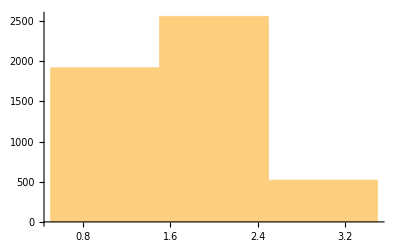

```mathematica
Histogram[countList]
```

```mathematica
ex=-(KK[2,3] (-2 KK[1,3] (1+CC[3] KK[1,3]) KK[2,2]+KK[1,2] (KK[2,3]+KK[1,3] (1+2 CC[3] KK[2,3]))))/(-4 KK[1,1] KK[1,3] KK[2,2] KK[2,3]+2 KK[1,2] (KK[1,3]^2 KK[2,2]+KK[1,1] KK[2,3]^2));
{a1,b1}=CoefficientList[Numerator[ex],CC[3]];
den = Denominator[ex];
(den - b1)/a1 //Simplify
```

(2 KK[1,3] (2 KK[1,1]+KK[1,3]) KK[2,2] KK[2,3]-2 KK[1,2] (KK[1,3]^2 KK[2,2]+KK[1,1] KK[2,3]^2+KK[1,3] KK[2,3]^2))/(KK[2,3] (-2 KK[1,3] KK[2,2]+KK[1,2] (KK[1,3]+KK[2,3])))

```mathematica
exprs
```

```mathematica
Collect[-(KK[2,3] (-2 KK[1,3] (1+CC[3] KK[1,3]) KK[2,2]+KK[1,2] (KK[2,3]+KK[1,3] (1+2 CC[3] KK[2,3])))),CC[3]]
Collect[-(KK[1,3] (-2 KK[1,1] KK[2,3] (1+CC[3] KK[2,3])+KK[1,2] (KK[2,3]+KK[1,3] (1+2 CC[3] KK[2,3])))),CC[3]]
```

-KK[2,3] (KK[1,2] KK[1,3]-2 KK[1,3] KK[2,2]+KK[1,2] KK[2,3])-CC[3] KK[2,3] (-2 KK[1,3]^2 KK[2,2]+2 KK[1,2] KK[1,3] KK[2,3])

-KK[1,3] (KK[1,2] KK[1,3]-2 KK[1,1] KK[2,3]+KK[1,2] KK[2,3])-CC[3] KK[1,3] (2 KK[1,2] KK[1,3] KK[2,3]-2 KK[1,1] KK[2,3]^2)

```mathematica
-KK[2,3] (KK[1,2] KK[1,3]-2 KK[1,3] KK[2,2]+KK[1,2] KK[2,3])//Simplify
```

-KK[2,3] (-2 KK[1,3] KK[2,2]+KK[1,2] (KK[1,3]+KK[2,3]))

```mathematica
Reduce[-(KK[2,3] (-2 KK[1,3] (1+CC[3] KK[1,3]) KK[2,2]+KK[1,2] (KK[2,3]+KK[1,3] (1+2 CC[3] KK[2,3]))))/(-4 KK[1,1] KK[1,3] KK[2,2] KK[2,3]+2 KK[1,2] (KK[1,3]^2 KK[2,2]+KK[1,1] KK[2,3]^2))>0,CC[3]]
```

```mathematica
(KK[2,3] (-2 KK[1,3] (1+CC[3] KK[1,3]) KK[2,2]+KK[1,2] (KK[2,3]+KK[1,3] (1+2 CC[3] KK[2,3]))))-(-4 KK[1,1] KK[1,3] KK[2,2] KK[2,3]+2 KK[1,2] (KK[1,3]^2 KK[2,2]+KK[1,1] KK[2,3]^2))//Simplify
```

-2 KK[1,3] (1-2 KK[1,1]+CC[3] KK[1,3]) KK[2,2] KK[2,3]+KK[1,2] (-2 KK[1,3]^2 KK[2,2]+(1-2 KK[1,1]) KK[2,3]^2+KK[1,3] KK[2,3] (1+2 CC[3] KK[2,3]))

```mathematica
KK[2,3] (-2 KK[1,3] (1+CC[3] KK[1,3]) KK[2,2]+KK[1,2] (KK[2,3]+KK[1,3] (1+2 CC[3] KK[2,3])))
```

```mathematica
exprs[[1]]/CC[1]//Simplify
```

CC[2] KK[1,2] KK[2,3]-KK[1,3] (1+CC[1] KK[1,2]+2 CC[2] KK[2,2]+CC[3] KK[2,3])

```mathematica
exprs=Adjugate[Qmat][[;;,mInd]];
Collect[exprs[[1]]/CC[1],Table[CC[i],{i,1,nd}]]
Collect[exprs[[2]]/CC[2],Table[CC[i],{i,1,nd}]]
(*Collect[exprs[[3]]/CC[3],Table[CC[i],{i,1,nd}]]*)
```

-KK[1,3]-CC[1] KK[1,2] KK[1,3]-CC[3] KK[1,3] KK[2,3]+CC[2] (-2 KK[1,3] KK[2,2]+KK[1,2] KK[2,3])

-KK[2,3]-CC[2] KK[1,2] KK[2,3]-CC[3] KK[1,3] KK[2,3]+CC[1] (KK[1,2] KK[1,3]-2 KK[1,1] KK[2,3])

```mathematica
Amat.vars-bvec
```

{0,0}

```mathematica
(*Define variables*)
vars={CC[1],CC[2],CC[3]};

kk=Flatten@Table[KK[i,j],{i,1,3},{j,1,3}];

Amat={{- KK[1,2] KK[1,3],  (-2 KK[1,3] KK[2,2]+KK[1,2] KK[2,3]),-KK[1,3] KK[2,3]},{(KK[1,2] KK[1,3]-2 KK[1,1] KK[2,3]),-KK[1,2] KK[2,3],- KK[1,3] KK[2,3]}};
bvec={KK[1,3],KK[2,3]};

y={yy[1],yy[2]};

farkasConditions={(Transpose[Amat].y)[[1]]>=0,(Transpose[Amat].y)[[2]]>=0,(Transpose[Amat].y)[[3]]>=0,bvec.y<0}
```

{-KK[1,2] KK[1,3] yy[1]+(KK[1,2] KK[1,3]-2 KK[1,1] KK[2,3]) yy[2]≥0,(-2 KK[1,3] KK[2,2]+KK[1,2] KK[2,3]) yy[1]-KK[1,2] KK[2,3] yy[2]≥0,-KK[1,3] KK[2,3] yy[1]-KK[1,3] KK[2,3] yy[2]≥0,KK[1,3] yy[1]+KK[2,3] yy[2]<0}

```mathematica
farkasConditions//MatrixForm
```

(-KK[1,2] KK[1,3] yy[1]+(KK[1,2] KK[1,3]-2 KK[1,1] KK[2,3]) yy[2]≥0
(-2 KK[1,3] KK[2,2]+KK[1,2] KK[2,3]) yy[1]-KK[1,2] KK[2,3] yy[2]≥0
-KK[1,3] KK[2,3] yy[1]-KK[1,3] KK[2,3] yy[2]≥0
KK[1,3] yy[1]+KK[2,3] yy[2]<0)

```mathematica
Manipulate[Plot[x/(x-a),{x,1,10},PlotRange->Full],{a,1,20}]
```

```mathematica
CoefficientList[lhs1,vars]
```

{{{-KK[1,3],-KK[1,3] KK[2,3]},{-2 KK[1,3] KK[2,2]+KK[1,2] KK[2,3],0}},{{-KK[1,2] KK[1,3],0},{0,0}}}

```mathematica
Amat
```

{{{{-KK[1,2] KK[1,3],0},{0,0}}},{{{KK[1,2] KK[1,3]-2 KK[1,1] KK[2,3],0},{0,0}}}}

```mathematica
Transpose[Amat].y//MatrixForm
```

((-KK[1,2] KK[1,3] yy[1]
0) | ((KK[1,2] KK[1,3]-2 KK[1,1] KK[2,3]) yy[1]
0))

#### Derivative space loop

```mathematica
ClearAll["Global`*"];


n= 3;
mInd = 1;
μ=1;
σ=3;

SeedRandom[32];

DeepRationalize[expr_,tol_:10^-12]:=expr/. r_Real:>Rationalize[r,tol]
ccSyms=Table[CC[i],{i,n}];
kkSyms=Flatten[Table[KK[i,j],{i,n},{j,n}]];

signCombos=Tuples[{1,-1},n];

Qf=Table[CC[i]*KK[i,j],{i,n},{j,n}];
Qd=DiagonalMatrix[Table[1+Sum[KK[i,j]*CC[j],{j,n}],{i,n}]];
symmetryRules=Flatten[Table[If[i>j,KK[i,j]->KK[j,i],Nothing],{i,n},{j,n}]];
Qmat=Qf+Qd/. symmetryRules;
QmatAdj=Adjugate[Qmat];

kValsList = {};
exprsList = {};
countList = {};


Do[

kValsT=RandomVariate[LogNormalDistribution[μ,σ],{n,n}];
kValsT=kValsT+1//Round;
Do[If[i>j,kValsT[[i,j]]=kValsT[[j,i]]],{i,n},{j,n}];
exprs=QmatAdj[[;;,mInd]]/. Thread[kkSyms->Flatten[kValsT]^-1]//Simplify;


AppendTo[kValsList,kValsT];
AppendTo[exprsList,exprs];

(*results=Table[{signCombo,
SemialgebraicComponentInstances[And@@Join[Table[DeepRationalize[exprs[[i]]]*signCombo[[i]]>0,{i,n}],Thread[ccSyms>0]],ccSyms]}
,{signCombo,signCombos}];*)

results = Table[{signCombo,
FindInstance[And@@Join[Table[exprs[[i]]*signCombo[[i]]>0,{i,n}],Thread[ccSyms>0]],ccSyms,Reals]}
,{signCombo,signCombos}];

count = 0;
Do[
If[Length[results[[r]][[2]]]>0,count+=1]
,{r,1,Length[results]}];
AppendTo[countList,count];

,{nxx,1,10}]//AbsoluteTiming
```

{0.213419,Null}

```mathematica
countList
```

{3,2,3,1,3,2,2,1,2,2}

```mathematica
{3,2,2,2,1,1,2,3,2,2}
```

```mathematica
FindInstance[And@@Join[Table[exprs[[i]]*signCombos[[15]][[i]]>0,{i,n}],Thread[ccSyms>0]],ccSyms,Reals]
```

{}

```mathematica
Length[signCombos]
```

16

```mathematica
exprs//Simplify//MatrixForm
```

((-1/16 CC[2] CC[3]+(1+CC[1]/11+2 CC[2]+CC[3]/4+CC[4]/73) (1+CC[1]/10+CC[2]/4+CC[3]+CC[4]/3)) (1+CC[1]/4+CC[2]/73+CC[3]/3+2 CC[4])-(CC[2] CC[4] (6 CC[1]+5 (12+3 CC[2]-61 CC[3]+4 CC[4])))/319740-(CC[3] CC[4] (292 CC[1]+11 (292+581 CC[2]+73 CC[3]+4 CC[4])))/28908
-(CC[2] (35040+876 CC[1]^2+120 CC[2]^2+37084 CC[3]+8468 CC[3]^2+80440 CC[4]+57694 CC[3] CC[4]+22920 CC[4]^2+2 CC[2] (4620+1634 CC[3]+8675 CC[4])+CC[1] (12264+2238 CC[2]+7519 CC[3]+9796 CC[4])))/385440
-(CC[3] (876 CC[1]^2+936 CC[2]^2+CC[1] (13140+17130 CC[2]+3577 CC[3]+4220 CC[4])+6 CC[2] (11476+3818 CC[3]+12151 CC[4])+22 (146 CC[3]^2+CC[3] (1022+519 CC[4])+4 (438+517 CC[4]+7 CC[4]^2))))/385440
-(CC[4] (876 CC[1]^2+48060 CC[2]^2+CC[1] (18396+21414 CC[2]+10001 CC[3]+3052 CC[4])+6 CC[2] (36055+28266 CC[3]+10735 CC[4])+22 (949 CC[3]^2+CC[3] (4891+417 CC[4])+20 (219+76 CC[4]+CC[4]^2))))/385440)

```mathematica
signCombos
```

{{1,1,1,1},{1,1,1,-1},{1,1,-1,1},{1,1,-1,-1},{1,-1,1,1},{1,-1,1,-1},{1,-1,-1,1},{1,-1,-1,-1},{-1,1,1,1},{-1,1,1,-1},{-1,1,-1,1},{-1,1,-1,-1},{-1,-1,1,1},{-1,-1,1,-1},{-1,-1,-1,1},{-1,-1,-1,-1}}

```mathematica
ClearAll["Global`*"];


n= 3;
mInd = 1;
μ=1;
σ=3;

SeedRandom[32];

DeepRationalize[expr_,tol_:10^-12]:=expr/. r_Real:>Rationalize[r,tol]
ccSyms=Table[CC[i],{i,n}];
kkSyms=Flatten[Table[KK[i,j],{i,n},{j,n}]];

signCombos=Tuples[{1,-1},n];

Qf=Table[CC[i]*KK[i,j],{i,n},{j,n}];
Qd=DiagonalMatrix[Table[1+Sum[KK[i,j]*CC[j],{j,n}],{i,n}]];
symmetryRules=Flatten[Table[If[i>j,KK[i,j]->KK[j,i],Nothing],{i,n},{j,n}]];
Qmat=Qf+Qd/. symmetryRules;
QmatAdj=Adjugate[Qmat];

kValsList = {};
exprsList = {};
countList = {};

Do[

kValsT=RandomVariate[LogNormalDistribution[μ,σ],{n,n}];
kValsT=kValsT+1//Round;
Do[If[i>j,kValsT[[i,j]]=kValsT[[j,i]]],{i,n},{j,n}];
div = ccSyms;
div[[1]]=1;
exprs=QmatAdj[[;;,mInd]]/div/. Thread[kkSyms->Flatten[kValsT]^-1]//Simplify;


AppendTo[kValsList,kValsT];
AppendTo[exprsList,exprs];


results = Table[{signCombo,
FindInstance[And@@Join[Table[exprs[[i]]*signCombo[[i]]>0,{i,2,n}],Thread[ccSyms>0]],ccSyms,Reals]}
,{signCombo,signCombos[[1;;16]]}];

count = 0;
Do[
If[Length[results[[r]][[2]]]>0,count+=1]
,{r,1,Length[results]}];
AppendTo[countList,count];

,{nxx,1,1}]//AbsoluteTiming
```

$Aborted

```mathematica
exprs[[2]]
```

1/18125026920(195 CC[3] (-292153 CC[4]+8268000 (1+CC[1]/4+CC[2]/53+CC[3]+(2 CC[4])/1945+CC[5]/78)) CC[5]-CC[4] CC[5] (355510+35551 CC[1]+4870 CC[2]+20946663 CC[3]+355510 CC[4]+355510 CC[5])+22737/2 CC[5] (170820 CC[3] CC[4]-22776 (1+CC[1]/4+CC[2]/53+CC[3]+(2 CC[4])/1945+CC[5]/78) (7 CC[3]-10 (1+CC[1]/10+CC[2]/73+2 CC[3]+CC[4]+CC[5]))-7 CC[4] (73 CC[1]+10 CC[2]+146 (8 CC[3]+5 (1+CC[4]+CC[5]))))+10647 (1+CC[1]/7+CC[2]+CC[3]+CC[4]/78+CC[5]/2) (148930 CC[3] CC[4]-212 (1+CC[1]/4+CC[2]/53+CC[3]+(2 CC[4])/1945+CC[5]/78) (730+73 CC[1]+10 CC[2]+1449 CC[3]+730 CC[4]+730 CC[5])+11 CC[4] (73 CC[1]+10 CC[2]+146 (8 CC[3]+5 (1+CC[4]+CC[5])))))

#### Derivative space loop numeric

```mathematica
ClearAll["Global`*"];
n= 6;
mInd = 1;
μ=1;
σ=5;

SeedRandom[42];


ccSyms=Table[CC[i],{i,n}];
kkSyms=Flatten[Table[KK[i,j],{i,n},{j,n}]];


Qf=Table[CC[i]*KK[i,j],{i,n},{j,n}];
Qd=DiagonalMatrix[Table[1+Sum[KK[i,j]*CC[j],{j,n}],{i,n}]];
symmetryRules=Flatten[Table[If[i>j,KK[i,j]->KK[j,i],Nothing],{i,n},{j,n}]];
Qmat=Qf+Qd/. symmetryRules;
QmatAdj=Adjugate[Qmat];

sampIter = 250;
cMax = 100;

kValsList = {};
exprsList = {};
countList = {};
countList2 = {};


Do[

kValsT=RandomVariate[LogNormalDistribution[μ,σ],{n,n}];
Do[If[i>j,kValsT[[i,j]]=kValsT[[j,i]]],{i,n},{j,n}];

exprs=QmatAdj[[;;,mInd]]/. Thread[kkSyms->Flatten[kValsT]^-1];
exprsEv=Function[{ccVec},exprs/. Thread[ccSyms->ccVec]];

signList = {};
Do[
cEvs=RandomReal[{0,cMax},{n}];
signs = Sign[exprsEv[cEvs]];
If[!MemberQ[signList,signs],AppendTo[signList,signs]];
,{iter,1,sampIter}];


AppendTo[kValsList,kValsT];
AppendTo[exprsList,exprs];
AppendTo[countList,Length[signList]];


,{nxx,1,200}]//AbsoluteTiming
```

{151.027,Null}

```mathematica
countList//Max
```

10

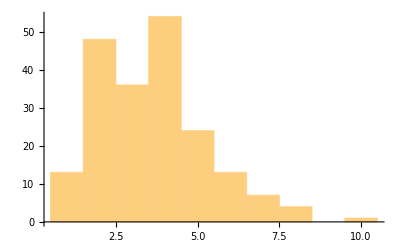

```mathematica
Histogram[countList]
```

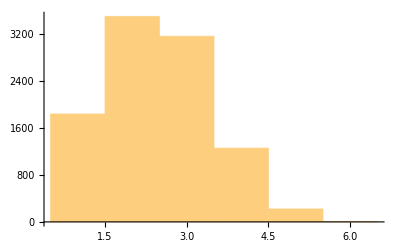

```mathematica
Histogram[countList]
```

```mathematica
countList//Max
```

9

```mathematica
n = 6;
ccSyms=Table[CC[i],{i,n}];
kkSyms=Flatten[Table[KK[i,j],{i,n},{j,n}]];


Qf=Table[CC[i]*KK[i,j],{i,n},{j,n}];
Qd=DiagonalMatrix[Table[1+Sum[KK[i,j]*CC[j],{j,n}],{i,n}]];
symmetryRules=Flatten[Table[If[i>j,KK[i,j]->KK[j,i],Nothing],{i,n},{j,n}]];
Qmat=Qf+Qd/. symmetryRules;
QmatAdj=Adjugate[Qmat];
QmatAdj[[1,1]]//MonomialList
minors = Map[Reverse,Minors[Qmat],{0,1}];
```